```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/data_v2/small_stepsize

```mathematica
chi2=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi2.dat"]],{i,800,960,1}];
chi4=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi4.dat"]],{i,800,960,1}];
r422=chi4/chi2;
```

```mathematica
mub=Table[i,{i,800,960,1}];
T=Table[i,{i,17,120,1}];
R42all=Flatten[Table[{x=mub[[j]],y=T[[i]],r422[[j]][[i]]},{i,1,Length[T]},{j,1,Length[mub]}],1];
(*Export["r42high.dat",R42all]*)
```

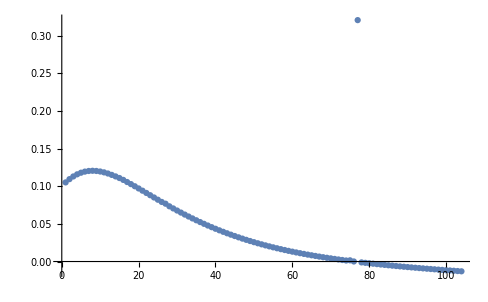

```mathematica
ListPlot[r422[[150]],PlotRange->{All,All}]
```

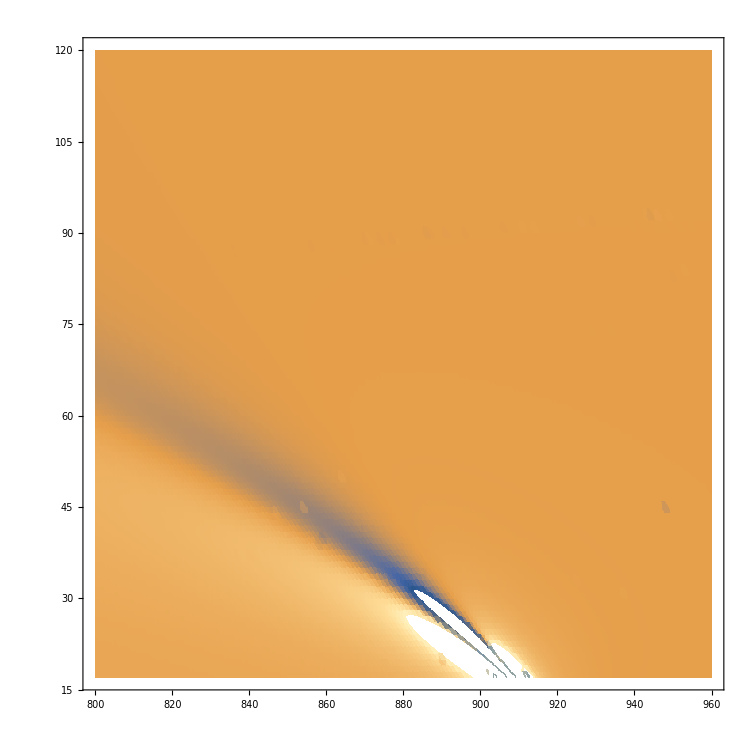

```mathematica
ListDensityPlot[R42all,PlotRange->{All,All,{-10,10}}]
```